# UpSetChart

```mathematica
Quit[]
```

#### Import UpSetChart

```mathematica
$Path=Prepend[$Path,NotebookDirectory[]];
<<UpSetChart`
```

## Quick Start

## Data

```mathematica
<<UpSetChart`TestData`
sets=DummyData[1];
```

## Plot

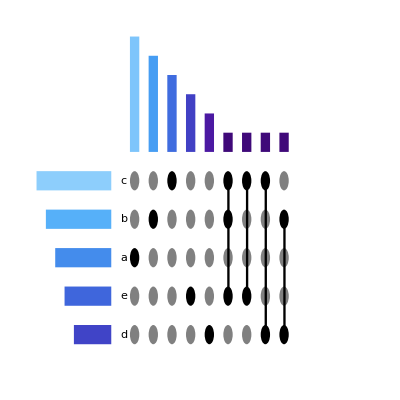

```mathematica
usc=UpSetChart[sets, "DropEmpty"->True,"TabbedByComparisonsDegreeQ"->False,
"ComparisonSortBy"->"Cardinality","SetSortBy"->"Cardinality",
ImageSize->{Automatic,400}
]
```

## Push the limits

```mathematica
twentySets=RandomData[20];
p=UpSetChart[
twentySets,
"DropEmpty"->True, 
"SetSortBy"->"Cardinality", "ComparisonSortBy"-> "Cardinality","TabbedByComparisonsDegreeQ"->True,"ImageSize"->{Automatic, 250}]
```

12345678

## Overview

#### Load Data

Some fixed dummy data sets are provided.

```mathematica
dd=UpSetChart`TestData`DummyData[3]
```

<|Red→{Strawberry,Apple},Green→{Kiwi,Pear,Cucumber,Pickle},Tasty→{Kiwi,Pear},Fruit→{Kiwi,Lemon,Banana,Strawberry,Pear,Apple,Carrot},Vegetable→{Cucumber,Pickle}|>

In addition data can be randomly generated.

```mathematica
rd=UpSetChart`TestData`RandomData[3, 10, 10]
```

<|a→{1,9,8,6,2},b→{5,10,4,9,6,2,3,0},c→{0,2,8,10}|>

#### Calculate elements unique to a comparison with `UniqueIntersections`

```mathematica
UpSetChart`UniqueIntersections`UniqueIntersections[rd]
```

<|sets→<|a→{1,9,8,6,2},b→{5,10,4,9,6,2,3,0},c→{0,2,8,10}|>,setNames→{a,b,c},comparisons→{{},{a},{b},{c},{a,b},{a,c},{b,c},{a,b,c}},numberOfSets→3,elementsUniqueToComparisons→<|{}→{},{a,b,c}→{2},{a,b}→{6,9},{a,c}→{8},{b,c}→{0,10},{a}→{1},{b}→{3,4,5},{c}→{}|>|>

#### CalcThenSortAndFilter chains together a common work flow

While Unique Intersections does all the calculations we need for this chart, the chart may want us to sort and filter results as well.
This “super” function does this.

```mathematica
UpSetChart`Calculations`CalcThenSortAndFilter[
rd,
"DropEmpty"->True, (* can be True or False *)
"ComparisonSortBy"->"Name", (* can be "Name" or "Cardinality" *)
"SetSortBy"->"Name", (* can be "Name" or "Cardinality" *)
"Verbose"->True (* can be True or False *)
]
```

<|sets→<|a→{1,9,8,6,2},b→{5,10,4,9,6,2,3,0},c→{0,2,8,10}|>,comparisons→<|{a}→{1},{b}→{3,4,5},{a,b}→{6,9},{a,c}→{8},{b,c}→{0,10},{a,b,c}→{2}|>|>

#### Utilities

Utilities contains several conditional checkers and helpers.

```mathematica
(* Conditionals for types & passing down options *)
<<UpSetChart`Utilities`
```

```mathematica
EnsureLabeledSets[{{1,2,3},{2,3,4,4,4}}]
```

<|a→{1,2,3},b→{2,3,4}|>

```mathematica
EnsureLabeledSets[{{},{}}]
```

<|a→{},b→{}|>

```mathematica
sets={{1,2,3},{2,3,4,4,4}};
ListOfListsQ[sets]
LabeledSetsQ[sets]
LabeledSetsQ[EnsureLabeledSets[sets]]
```

True

False

True

## Dynamic if you dare

```mathematica
(* This is resource intensive *)
DynamicUpSetChart[sets]
```